```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Inside Fourier Transforms

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

The spectrum gives important information about the makeup of a signal. This notebook contains some of the details of how and why it works.

```mathematica
TableForm[{{Hyperlink["FFTMatrix",{"vvFourierAngles.nb","labelFFTMatrix"},BaseStyle->mathColor],labelFFTMatrix},{Hyperlink["FFTOrth",{"vvFourierAngles.nb","labelFFTOrth"},BaseStyle->mathColor],labelFFTOrth},{Hyperlink["FFT2Sines",{"vvFourierAngles.nb","labelFFT2Sines"},BaseStyle->mathColor],labelFFT2Sines},{Hyperlink["FrequencyResponse",{"vvFourierAngles.nb","labelFreqResp"},BaseStyle->mathColor],labelFreqResp}}]
```

| The DFT matrix consists of rows of (complex-valued) sinusoids
 | The inner product between different rows of the DFT matrix is zero
 | The Fourier transform (spectrum) of the dual sinusoidal signal shows peaks at each of the two frequencies
 | Convolution in the time domain is equivalent to multiplication in the frequency domain

The way the (discrete) Fourier transform works is to compare a sinusoid of one frequency to the data sequence. Then to compare a second. Then a third, continuing all the way up to the highest frequency that can be represented by the length of the data. Then all these comparisons are placed into a list called the spectrum. In the figure below, the green sequence x represents the data that is to be analyzed. The rows of yellow w’s represent the different frequency sinusoids, starting with frequency 0 (all 1’s) followed by a frequency that fits one sine wave cycle into the length of the data, then by a frequency that fits two sine cycles into the same length, then three, etc., all the way up to N-1. The correlation (or inner product) of these sinusoids and the data sequence are stored up as the blue sequence on the right.

```mathematica
Column[{Image[-Graphics-, ImageSize -> 800] , 
  Style["The Fourier transform can be pictured as a collection of inner products between the data (green) and a collection of sinusoids (yellow). The output is a new sequence, called the spectrum (blue)..", captionStyle]}, Alignment -> Center](* 1dimCorrelation.ai *)
```

-Graphics-
The Fourier transform can be pictured as a collection of inner products between the data (green) and a collection of sinusoids (yellow). The output is a new sequence, called the spectrum (blue)..

The figure above shows that the (discrete) Fourier Transform operates on a sequence x[k] of length N and returns another sequence X[n] of length N.  Translating the above figure into symbols, the DFT is defined by

X[n]=∑_(k=0)^(N-1) x[k]e^(-(2inkπ)/N)for n=0,1,...,N-1

which is the same as the inner product <x, e^((2 ⅈ π nk)/N)> between the vector x and the (complex-valued) sinusoid e^((2 ⅈ π nk)/N). For each value n, the DFT multiplies each term of the data x by the complex exponential and then sums. There are several things worth observing about this. First, consider the sinusoidal element(s). Each of the vectors is of size N, each is of (normalized) frequency n/N and contains N elements indexed from k = 0 , 1, ... , N-1. These vectors are called sinusoids because of Euler’s formula, which rewrites the complex exponential form into trigonometric form:

```mathematica
Row[{ExpToTrig[Exp[I θ]],Spacer[100],ExpToTrig[Exp[-2 Pi I n k/N]]}]
```

Cos[θ]+ⅈ Sin[θ]Cos[(2 k n π)/N]-ⅈ Sin[(2 k n π)/N]

For example, with N=8, the lowest frequency term corresponds to n=0, which is the “DC” or zero frequency term

```mathematica
W[Nterms_,n_,k_]:=Exp[-2 Pi I n k/Nterms];
W[8,0,Range[8]-1]
```

{1,1,1,1,1,1,1,1}

More interesting is the n=1 vector:

```mathematica
w1=W[8,1,Range[8]-1]
```

{1,ⅇ^(-(ⅈ π)/4),-ⅈ,ⅇ^(-(3 ⅈ π)/4),-1,ⅇ^((3 ⅈ π)/4),ⅈ,ⅇ^((ⅈ π)/4)}

Translating this from complex form into real-imaginary form gives

```mathematica
ExpToTrig[w1]
```

{1,(1-ⅈ)/(√2),-ⅈ,-(1+ⅈ)/(√2),-1,-(1-ⅈ)/(√2),ⅈ,(1+ⅈ)/(√2)}

which can be plotted as two separate plots, one for the real part and one for the imaginary part.

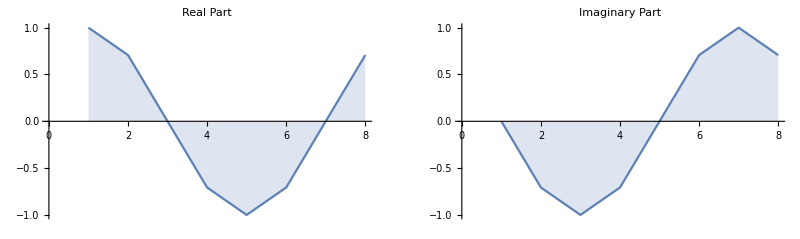

```mathematica
GraphicsRow[{ListLinePlot[Re[w1],PlotLabel->"Real Part",Filling->Axis] ,ListLinePlot[Im[w1],PlotLabel->"Imaginary Part",Filling->Axis]}]
```

These are nothing more than plots of the Cos[ ] and (minus) the Sin[ ] functions sampled N=8 times per period. This can be done for any N. Each row of the following matrix is one of these vectors.

```mathematica
labelFFTMatrix="The DFT matrix consists of rows of (complex-valued) sinusoids";
infoFFTMatrix="The slider changes the order (size) of the DFT matrix. This matrix has a lot of structure:\n\nIt always has a row of ones across the top and a row of ones down the first column.\n\nIt is symmetric.\n\nEach column (and each row) is a complex-valued sinusoid with frequencies that subdivide the total length.\n\nEach column (and each row) are orthogonal to all the others.";
Manipulate[Table[W[Nterms,n,k],{k,0,Nterms-1},{n,0,Nterms-1}]//TableForm,Row[{Control[{{Nterms,8,"number of terms"},1,32,1,Appearance->"Labeled"}],Spacer[20],info[infoFFTMatrix]}],
FrameLabel->Style[labelFFTMatrix,Medium],TrackedSymbols->{Nterms},SaveDefinitions->True]
```

Moreover, each row is orthogonal to every other row. Here is a direct verification of this for any N up to 80 (though of course it is true for all N). Whenever n is different from m,  the inner product between the two rows is zero. When n=m, the inner product is equal to N (in the demonstration, both are divided by N, so the resulting sum is 1).

```mathematica
labelFFTOrth="The inner product between different rows of the DFT matrix is zero";
infoFFTOrth="The length slider sets the length of the complex sinusoids.\n\nThe two frequency sliders choose two different frequencies, and the real parts of these signals are plotted.\n\nThe inner product between the two (complex-valued) signals is calculated directly and then simplified (using Mathematica's symbolic manipulations and the FullSimplify[] function).\n\nThe answer to this inner product is either 1 (when the two frequencies are the same) or 0 (when the two frequencies are different).";
Manipulate[Column[{GraphicsRow[{ListLinePlot[Re[W[Nterms,n,Range[Nterms]-1]],Filling->Axis,PlotLabel->"Real Part Frequency n = "~~ToString[n]],ListLinePlot[Re[W[Nterms,m,Range[Nterms]-1]],Filling->Axis,PlotLabel->"Real Part Frequency m = "~~ToString[m]]},ImageSize->500],Framed[Row[{W[Nterms,n,Range[Nterms]-1].Conjugate[W[Nterms,m,Range[Nterms]-1]/Nterms],"  =  ",FullSimplify[Inner[Times,W[Nterms,n,Range[Nterms]-1],Conjugate[W[Nterms,m,Range[Nterms]-1]],Plus]/Nterms]}]]}],
Row[{Control[{{Nterms,20,"length of signal"},1,80,1,Appearance->"Labeled"}],Spacer[20],info[infoFFTOrth]}],
{{n,1,"frequency "~~ToString[n]},0,Nterms-1,1,Appearance->"Labeled"},{{m,2,"frequency "~~ToString[m]},0,Nterms-1,1,Appearance->"Labeled"},
FrameLabel->Style[labelFFTOrth,Medium],TrackedSymbols->{Nterms,n,m},SaveDefinitions->True]
```

Summarizing the results shown above in words is easy. (Complex) sinusoids of different frequencies are orthogonal (are at right angles, are uncorrelated with each other). Sinusoids of the same frequency point in the same direction, lie at an angle of zero degrees to each other. Considering it in this light presents a compelling interpretation of the Fourier transform (or more properly, the DFT). First, X[n] is a function of frequency: for each n the inner product is evaluated to give a complex-valued number with magnitude m and angle θ. Since X[n] is the correlation (inner product) between the signal x and a sinusoid of frequency 2πn/N, values of the correlation where m is large show the frequencies of the sine wave is “close to” x. Since sine waves of different frequencies are orthogonal, there is no interaction between different frequencies, and m is the amount of the frequency 2πn/N present in the signal x. The Fourier transform shows how x can be uniquely decomposed into (and rebuilt from) sums of sinusoids.

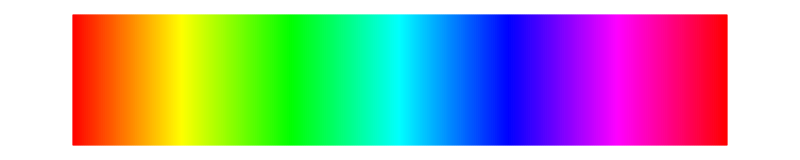

```mathematica
specLine
```

In many common applications, the Fourier transform is used to locate the frequencies in a signal. For example, if t is a time variable, the following shows the sum of two sinusoids with frequencies 10.7 and 17.2 Hz, plotted over one second.

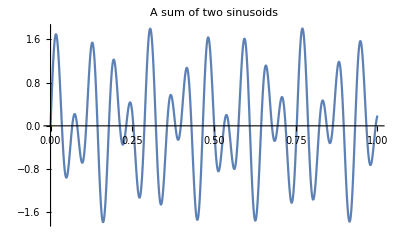

```mathematica
f[t_]:=Sin[2 Pi 17.2 t]+0.8 Sin[2 Pi 10.7 t];
Plot[f[t],{t,0,1},PlotLabel->"A sum of two sinusoids"]
```

For those who have had a course in Signals and Systems, the continuous-time Fourier transform of a signal x[t] is the integral

```mathematica
Clear[x]; Integrate[x[t] Exp[-ω t I] ,{t,-Infinity,Infinity}]
```

∫_(-∞)^∞ ⅇ^(-ⅈ t ω) x[t]ⅆt

For the case where x[t] is the two-sinusoid function above, this can be calculated efficiently using

```mathematica
Chop[FourierTransform[f[t],t,ω]]
```

(0.+1.00265 ⅈ) DiracDelta[67.2301-ω]+ⅈ √(π/2) DiracDelta[108.071-ω]-(0.+1.00265 ⅈ) DiracDelta[67.2301+ω]-ⅈ √(π/2) DiracDelta[108.071+ω]

which shows that the Fourier Transform of these two sinusoids is a sum of delta functions which occur at +/- 67.2 (=2 Pi 10.7) and +/-108.07 (=2 Pi 17.2). Such analytic forms will only be useful if there is a formula-based definition for the signal. In this case, there is, and Mathematica’s symbolic processing can carry out the calculations easily.

Since in data analysis the signals are sampled, there is no functional form, and it is necessary to use the discrete form. The same signal f[t] above can be sampled at 1000 times per second and then analyzed by the FFT. The first plot shows the magnitude of the full 1000-point output, while the second zooms in to the lowest frequencies. The peaks near 11 and 17 are clear in the zoomed in version. The set of peaks out near 1000 in the left=hand plot are the "negative" frequencies (the mirror image of the positive frequencies, just as in the analytic solution above).

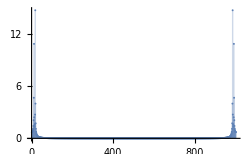
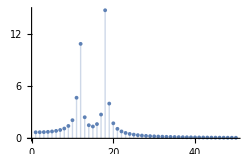
-Graphics--Graphics-The Fourier transform (spectrum) of the sinusoidal signal shows peaks at each of the two frequencies

```mathematica
sampF=Table[f[t],{t,0,1,1/1000}];
Labeled[Row[{ListPlot[Abs[Fourier[sampF]],PlotRange->All,Filling->Axis,ImageSize->250],Spacer[20],
ListPlot[Abs[Fourier[sampF]][[1;;50]],PlotRange->All,Filling->Axis,ImageSize->250]}],"The Fourier transform (spectrum) of the sinusoidal signal shows peaks at each of the two frequencies",LabelStyle->captionStyle]
```

Here is the same idea done more generally to give an idea of how things change as the parameters of the signal change.

```mathematica
labelFFT2Sines="The Fourier transform (spectrum) of the dual sinusoidal signal shows peaks at each of the two frequencies";
infoFFT2Sines="The signal (top left) is a sum of two sinusoids with frequencies speciied by the two sliders. The third slider controls the relative amplitude of the  two sines.\n\nThe top right shows the analytical solution of the Fourier transform. While interesting enough, this is probably the last time we will look at this kind of thing. (So it's probably best just to ignore it).\n\nThe bottom left shows the FFT of the sampled signal (i.e., the magnitude spectrum). It's hard to see because all the useful information is squished to the left. There's also a mirror image of the information on the right. For technical reasons (see the notebook 'inside Fourier transforms' if this interests you) this is always present. But since it's just a copy of the low frequency information, it's reasonable to ignore the right half of the spectrum. \n\nThe bottom right figure zooms into the spectrum. \n\nThe peaks of the spectrum show the frequencies of the sinusoids.\n\nChange the frequencies; observe how the peaks in the spectrum move left and right as a result. \n\nChange the amplitude of the sines; observe how the height of the peaks changes in response.";
Manipulate[sampF=Table[fSins[t,f1,f2,a],{t,0,1,1/1000}];GraphicsGrid[{{Plot[fSins[t,f1,f2,a],{t,0,1}],FourierTransform[fSins[t,f1,f2,a],t,ω]},
{ListPlot[Abs[Fourier[sampF]],PlotRange->All,Filling->Axis,PlotLabel->"Fourier Transform"],ListPlot[Abs[Fourier[sampF]][[2;;50]],PlotRange->All,Filling->Axis,PlotLabel->"zoom into Fourier Transform"]}},ImageSize->600],{{f1,17.2,"frequency of first sinusoid"},1,50,Appearance->"Labeled"},{{f2,10.7,"frequency of second sinusoid"},1,50,Appearance->"Labeled"},
Row[{Control[{{a,0.8,"relative amplitude"},0,2,Appearance->"Labeled"}],Spacer[20],info[infoFFT2Sines]}],
FrameLabel->Style[labelFFT2Sines,Medium],TrackedSymbols->{f1,f2,a},SaveDefinitions->True,Initialization->(fSins[t_,ω1_,ω2_,a_]:=Sin[2 Pi ω1 t]+a Sin[2 Pi ω2 t])]
```

Let’s interpret the features of the above figure. Since the time period is 1 second, the frequency f1 specifies the number of sinusoidal periods over that one second. When f1=17.2, there are exactly 17.2 sinusoidal undulations in the plot (turn the amplitude to zero to see it more clearly, or change f1 to an integer to make it easier to count). Similarly for f2, the frequency shown by the FFT describes the number of sinusoidal periods over the time extent of the data. When both occur together, the figure says that the best-fit sinusoid to the data has f1 periodic undulations over the duration of the signal while the next best-fit sinusoid has f2 periodic undulations over the extent of the signal. Moreover, the heights of the peaks are significant: the largest peak corresponds to the strongest (largest) sinusoid (experiment with this by adjusting the amplitude value).

Observe also that the Fourier transform is invertible. The inversion formula

x[k]=1/N∑_(n=0)^(N-1) e^((2inkπ)/N)X[n]fork=0,1,...,N-1

reverses the role of the time and frequency variables and ensures that the transform neither creates nor destroys information. The inversion is most simply applied in Mathematica using InverseFourier[ ]. The combination of the transform and its inverse can be used to implement any linear filter. The procedure is: (1) take the DFT of the signal (2) modify the spectrum  X[n] (for instance, by setting some terms to zero or weighting some of the terms) (3) take the inverse. The resulting output is the filtered signal.

### The Frequency Response of a Linear System

The Fourier transform has another important interpretation. The frequency response of linear filter W[n] is a function of frequency that defines how the spectrum X[n] of the input is changed into the spectrum Y[n] of the output. The frequency response and the impulse response w[k] (i.e, the kernel of the filter) are intimately related: W[n] is the Fourier transform of w[k]. Sometimes W[n] is called the transfer function, because W[n] = Y[n]/X[n]. Thus at any given frequency (say some value n*), a sinusoid of frequency n* in the input has magnitude |X[n*]|. The transfer function has magnitude |W[n*]| and so the output has magnitude Y[n*]=W[n*] X[n*]. This is shown experimentally in the following demonstration. A random data set x[k] is generated and it’s spectrum is calculated, as shown in green. The impulse response (kernel) of the filter and its spectrum are shown in yellow. The action of the filter is the convolution of x and w, which is hard to visualize. But the action of the filter in the frequency domain is just the point-by-point multiplication of the spectrum X[n] and the frequency response W[n]. Note how when W[n] is large, the spectrum of the output wiggles in synchrony with the spectrum of the input, when W[n] is small, the same wiggles occur but greatly attenuated. Y[n] is simply the product of the two curves above.

```mathematica
labelFreqResp="Convolution in the time domain is equivalent to multiplication in the frequency domain";
infoFreqResp="The spectra of the same five linear filters (impulse responses) are shown here.\n\nThe spectrum of the input is calculated using the Fourier[ ] command and the spectrum of the impulse response is calculated using the freqZ[ ] command (which is itself based on Fourier[ ]).\n\nObserve that in each case, the point by point product of these two spectra is equal to the spectum Y[n] of the output signal y[k].\n\nEach time new input data is created (with the 'regenerate data' button) the details of the specta of X[n] and Y[n] change but the overall shape remains the same.\n\nThe frequency responses make it easy to name the filters: the impulse responses 1 and 3 correspond to frequency responses with a lowpass character. Impulse responses 2 and 4 correspond to frequency responses with a highpass character and impulse response 5 is a kind of bandpass filter.";
numImp=5;imp=ConstantArray[{},numImp]; imp[[1]]={1,1,1}; imp[[2]]={-1/2,1,-1/2}; imp[[3]]={1,1,1,1,1};
imp[[4]]={1/4,-1/3,1/2,-1,1/2,-1/3,1/4};imp[[5]]:={1,1/2,-2,1/2,1};
data64=RandomChoice[{-1,1},64];
shiftImp[len_,pos_,impRes_]:=Flatten[{ConstantArray[0,pos-1],impRes,ConstantArray[0,len-pos-Length[impRes]+1]}];
Manipulate[impVec=shiftImp[64,30,imp[[ord]]];
If[r==1,data64=RandomChoice[{-1,1},64];r=0];
filtOut=ListConvolve[Reverse[imp[[ord]]],data64];
Column[{Row[{ListPlot[data64,Filling->Axis,PlotStyle->Green,FillingStyle->Green,PlotLabel->"Data x[k]",AspectRatio->1/3,ImageSize->300],Spacer[30],Plot[Abs[freqZ[data64,w]],{w,-1,1},ImageSize->300,PlotStyle->Green,AspectRatio->1/3,PlotLabel->"Spectrum of Data X[n]"]}],Spacer[10],
Row[{ListPlot[impVec,Filling->Axis,PlotStyle->darkYellow,FillingStyle->darkYellow,PlotLabel->"Impulse Response w[k]",AspectRatio->1/3,ImageSize->300,PlotLabel->"Impulse Response h[i]"],Spacer[30],Plot[Abs[freqZ[imp[[ord]],w]],{w,-1,1},ImageSize->300,PlotStyle->darkYellow,AspectRatio->1/3,PlotRange->All,PlotLabel->"Frequency Response W[n]"]}],Spacer[10],
Row[{ListPlot[filtOut,Filling->Axis,PlotStyle->Blue,PlotLabel->"Filtered Output y[k]",AspectRatio->1/3,ImageSize->300],Spacer[30],Plot[Abs[freqZ[filtOut,w]],{w,-1,1},ImageSize->300,PlotRange->All,PlotStyle->Blue,AspectRatio->1/3,PlotLabel->"Spectrum of Output Y[n]"]}]}],
Row[{Control[{{r,1,""},Button["Regenerate Data",r=1]&}],Spacer[20],Control[{{ord,1,"impulse response"},Range[numImp],ControlType->"PopupMenu"}],Spacer[20],info[infoFreqResp]}],
FrameLabel->Style[labelFreqResp,Medium],TrackedSymbols->{r,ord},SaveDefinitions->True]
```

This observation is important for two reasons. First, it allows us to talk about the action of a filter in concrete terms: a low pass filter is one that passes low frequencies and attenuates high frequencies, a bandpass filter is one that passes a range of frequencies and attenuates others, etc. The character of the filter can be seen directly from the shape of the frequency response. Second, the equivalence of the left hand column and the right hand column of the above figure means that the filtering operation can be accomplished (if desired) purely in the time domain, or purely in the frequency domain, whichever is more convenient. And often it is easiest to flip back and forth between the two domains.

### Fourier Transform in Two DImensions

Suppose x[i,j] is a two-dimensional signal such as an image where i=1, 2, ... Ni and j=1, 2, ... Nj. The Discrete Fourier Transform (DFT) is defined to be

```mathematica
X[s_, t_] := ∑_(i=0)^(Ni-1)  ∑_(j=0)^(Nj-1) x[[i+1,j+1]] E^(-I 2 Pi (s i/Ni +t j/Nj));
```

where s and t range over Ni and Nj respectively. Observe that this is really just two independent copies of the one-dimensional definition. For example, suppose the signal x is

```mathematica
x=RandomReal[{0,1},{4,6}];
{Ni,Nj}=Dimensions[x];
MatrixForm[x]
```

(0.715849 | 0.34042 | 0.787328 | 0.892824 | 0.753489 | 0.299
0.811026 | 0.240304 | 0.331094 | 0.276579 | 0.3411 | 0.332318
0.851281 | 0.438827 | 0.258603 | 0.481311 | 0.015321 | 0.00168839
0.886514 | 0.561603 | 0.700422 | 0.692741 | 0.559767 | 0.877021)

Then for each s and t, the DFT of x is X[s,t] as given by the formula above. One way to calculate this directly:

```mathematica
Table[X[s,t],{s,0,Ni-1},{t,0,Nj-1}]//MatrixForm
```

(12.4464 | 0.593244-0.414737 ⅈ | 2.18897+0.291542 ⅈ | 1.57716 | 2.18897-0.291542 ⅈ | 0.593244+0.414737 ⅈ
1.74188+1.94565 ⅈ | -1.14394+0.322415 ⅈ | -0.780767-0.0740277 ⅈ | 0.521043-0.61868 ⅈ | -0.132867-0.396666 ⅈ | -1.01794-0.725754 ⅈ
-0.774549 | -0.942059-0.894139 ⅈ | 0.798881-0.640442 ⅈ | 0.278443 | 0.798881+0.640442 ⅈ | -0.942059+0.894139 ⅈ
1.74188-1.94565 ⅈ | -1.01794+0.725754 ⅈ | -0.132867+0.396666 ⅈ | 0.521043+0.61868 ⅈ | -0.780767+0.0740277 ⅈ | -1.14394-0.322415 ⅈ)

Another (easier) way is to use the built-in function Fourier[ ]

```mathematica
Xfx=Fourier[x,FourierParameters->{1,-1}];
MatrixForm[Xfx]
```

(12.4464+0. ⅈ | 0.593244-0.414737 ⅈ | 2.18897+0.291542 ⅈ | 1.57716+0. ⅈ | 2.18897-0.291542 ⅈ | 0.593244+0.414737 ⅈ
1.74188+1.94565 ⅈ | -1.14394+0.322415 ⅈ | -0.780767-0.0740277 ⅈ | 0.521043-0.61868 ⅈ | -0.132867-0.396666 ⅈ | -1.01794-0.725754 ⅈ
-0.774549+0. ⅈ | -0.942059-0.894139 ⅈ | 0.798881-0.640442 ⅈ | 0.278443+0. ⅈ | 0.798881+0.640442 ⅈ | -0.942059+0.894139 ⅈ
1.74188-1.94565 ⅈ | -1.01794+0.725754 ⅈ | -0.132867+0.396666 ⅈ | 0.521043+0.61868 ⅈ | -0.780767+0.0740277 ⅈ | -1.14394-0.322415 ⅈ)

which is the same (except for some rounding issues). Since the DFT is complex valued, it is common to plot it as two images, one for the magnitude and one for the phase.

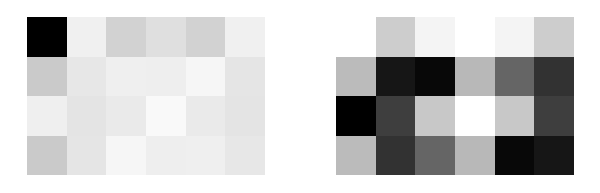
-Graphics-Plotting the magnitude and phase of the DFT as two grayscale images

```mathematica
Labeled[GraphicsRow[{ArrayPlot[Abs[Xfx]],ArrayPlot[Arg[Xfx]]},ImageSize->600],"Plotting the magnitude and phase of the DFT as two grayscale images",LabelStyle->captionStyle]
```

Of course, this can be done for any size matrix or image. For more applications of the 2D Fourier transform, see the notebook on thread counting via the Fourier transform.